```mathematica
(*upper bound of simple representation asymptotic*)
FullSimplify[Asymptotic[Binomial[n,n/2],n->Infinity]]
```

2^(1/2+n)/(√n √π)

```mathematica
(*lower bound*)
FullSimplify[Asymptotic[FunctionExpand[Binomial[n,n/2-Sqrt[2n]]],n->Infinity]]
```

(2^(1/2+n) ⅇ^(-4-16/(3 n)))/(√n √π)

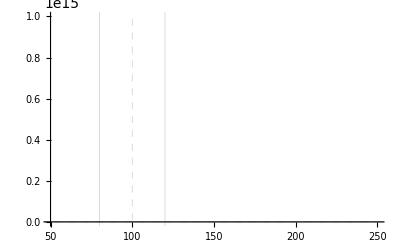

```mathematica
(*Plot of simple rep size for n=200 to truncate*)
DiscretePlot[Binomial[200,k],{k,50,250},PlotRange->All,GridLines->{{{200/2-Sqrt[2*200],Thick},{200/2+Sqrt[2*200],Thick},{200/2,Dashed}}}]
```

```mathematica
(*peak of the monoid compared with the truncation*)
DiscretePlot[{Sum[Binomial[k+1,2j+1]*Binomial[200+j,k]^2,{j,0,Floor[k/2]}]},{k,50,250},PlotRange->All,GridLines->{{{200/2-Sqrt[2*200],Thick},{200/2+Sqrt[2*200],Thick},{200/2,Dashed}}}]
```

-Graphics-

```mathematica
(*upper bound for gap ratio*)
FullSimplify[Asymptotic[Binomial[n,n/2]/Binomial[5n/4,n/2],n->Infinity]]
```

√(6/5) ⅇ^(1/4 n (-5 Log[5]+Log[1728]))

```mathematica
FullSimplify[E^(Log[5^(-5n/4)])*E^(Log[1728^(n/4)])]
```

2^(3 n/2) 3^(3 n/4) 5^(-5 n/4)

```mathematica
(*exponential growth factor of the size of the monoid for n=500*)
N[Sum[Sum[Binomial[k+1,2j+1]*Binomial[500+j,k]^2,{j,0,Floor[k/2]}],{k,0,2*500}]^(1/500)]
```

8.93039

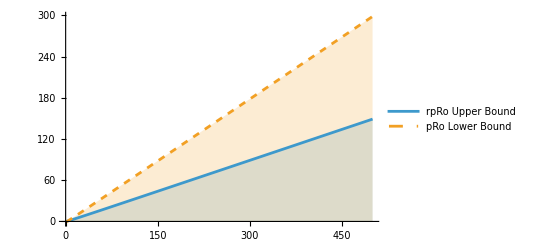

```mathematica
(*comparison of the representation gaps for pivotal vs non-pivotal*)
DiscretePlot[{Log10[2^(1/2+n)/(√n √π)],Log10[2^(2n)*n^(-1/2)*Pi^(-1/2)*E^(-2-1/(3n))]},{n,0,500},PlotLegends->{"rpRo Upper Bound","pRo Lower Bound"},PlotStyle->{Automatic,Dashed}]
```

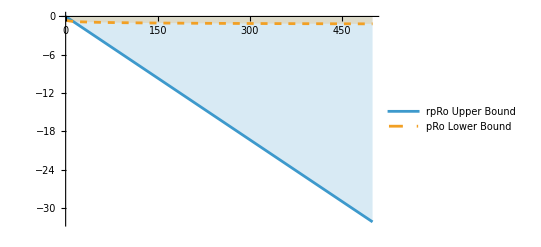

```mathematica
(*comparison of the gap ratios for pivotal vs non-pivotal*)
DiscretePlot[{Log10[2^(3 n/2) 3^(3 n/4) 5^(-5 n/4)],Log10[2^(1/4)*Pi^(-1/4)*E^(-1-1/(3n))*n^(-1/4)]},{n,0,500},PlotRange->All,PlotLegends->{"rpRo Upper Bound","pRo Lower Bound"},PlotStyle->{Automatic,Dashed}]
```